```mathematica
$PlotTheme="Scientific"
```

Scientific

```mathematica
SetOptions[{Plot,ListPlot,ArrayPlot,ContourPlot,DiscretePlot3D},BaseStyle->{14,Directive[FontFamily->"cmr10"]}];
```

# Immirzi 0.1 and i_b=0

## Load the Data

```mathematica
SetDirectory[NotebookDirectory[]]
```

/home/pdona/Dropbox/Ongoing Projects/OtherEPRLDivergences/Spinfoam_radiative_corrections/Notebooks

```mathematica
DATA = "../data/EPRL/immirzi_0.1/divergence/cutoff_10.0/self_energy_2_Dl_min_0_Dl_max_10.csv";
```

```mathematica
{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10}=Transpose@Import[DATA,"Data",HeaderLines->1];
```

```mathematica
{AKDl0,AKDl1,AKDl2,AKDl3,AKDl4,AKDl5,AKDl6,AKDl7,AKDl8,AKDl9,AKDl10} = Table[{k,#[[2k+1]]},{k,0,10,1/2}]&/@{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10};
```

## Extrapolation using Series convergence acceleration

```mathematica
Aitken[AD_]:=(AD[[-1]]AD[[-3]]-AD[[-2]]^2)/(AD[[-1]]-2AD[[-2]]+AD[[-3]])
```

```mathematica
rExtrapolation= Aitken/@Transpose[{rAKDl0,rAKDl1,rAKDl2,rAKDl3,rAKDl4,rAKDl5,rAKDl6,rAKDl7,rAKDl8,rAKDl9,rAKDl10}]
```

{7.01307×10^-8,7.33784×10^-8,7.41187×10^-8,7.51279×10^-8,7.52185×10^-8,7.52377×10^-8,7.52439×10^-8,7.52463×10^-8,7.52475×10^-8,7.5248×10^-8,7.52483×10^-8,7.52485×10^-8,7.52486×10^-8,7.52487×10^-8,7.52487×10^-8,7.52488×10^-8,7.52488×10^-8,7.52488×10^-8,7.52488×10^-8,7.52488×10^-8,7.52488×10^-8}

```mathematica
Extrapolation=Join[{{0,0}},Table[{k,#[[2k+1]]},{k,1/2,10,1/2}]&@rExtrapolation]
```

{{0,0},{1/2,7.33784×10^-8},{1,7.41187×10^-8},{3/2,7.51279×10^-8},{2,7.52185×10^-8},{5/2,7.52377×10^-8},{3,7.52439×10^-8},{7/2,7.52463×10^-8},{4,7.52475×10^-8},{9/2,7.5248×10^-8},{5,7.52483×10^-8},{11/2,7.52485×10^-8},{6,7.52486×10^-8},{13/2,7.52487×10^-8},{7,7.52487×10^-8},{15/2,7.52488×10^-8},{8,7.52488×10^-8},{17/2,7.52488×10^-8},{9,7.52488×10^-8},{19/2,7.52488×10^-8},{10,7.52488×10^-8}}

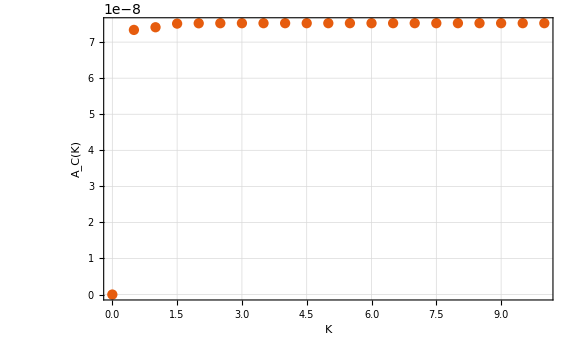

```mathematica
ListPlot[Extrapolation,PlotRange->All,GridLines->Automatic,FrameLabel->{"K","A_C(K)"},ImageSize->Large]
```

```mathematica
fitExtrap=NonlinearModelFit[Extrapolation[[5;;]], a Log[k] +b + c/k +d/k^2 ,{a,b,c,d},k]
```

FittedModel[7.51483×10^-8-(5.23478×10^-10)/k^2+(3.60674×10^-10)/k+3.04658×10^-11 Log[k]]

```mathematica
fitExtrap=NonlinearModelFit[Extrapolation[[5;;]],b + c/k +d/k^2 ,{b,c,d},k]
```

FittedModel[7.52406×10^-8-(2.8224×10^-10)/k^2+(9.98524×10^-11)/k]

```mathematica
fitExtrap["ParameterConfidenceIntervals"]
```

{{7.52378×10^-8,7.52434×10^-8},{7.58439×10^-11,1.23861×10^-10},{-3.24505×10^-10,-2.39976×10^-10}}

```mathematica
fit1 =First/@fitExtrap["ParameterConfidenceIntervals"].{1,1/k , 1/k^2};
fit2 =Last/@fitExtrap["ParameterConfidenceIntervals"].{1,1/k , 1/k^2};
```

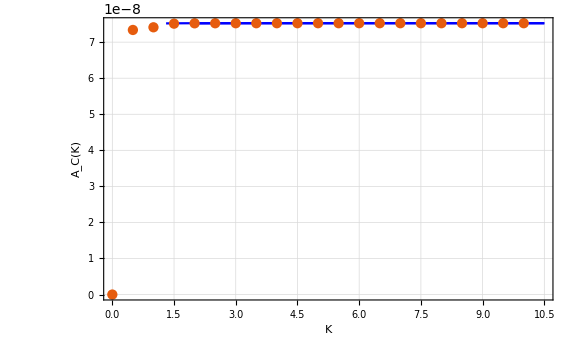

```mathematica
Show[Plot[{fit1,fit2},{k,1,10.5},PlotStyle->Blue,Filling->{1->{2}},GridLines->Automatic,FrameLabel->{"K","A_C(K)"},ImageSize->Large],ListPlot[Extrapolation,PlotRange->All],PlotRange->All]
```